## τα from fitting CRSISF, SISF to stretched exponential

```mathematica
(*saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";*)
```

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p382/";
```

```mathematica
Directory[]
```

/home/chengling

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

## longest times when τα belongs (1000,10000)

### check if we equilibrate long enough

```mathematica
Tlist={0.063, 0.039 ,0.03105 ,0.025, 0.016 ,0.01, 0.008 ,0.0063, 0.005 ,0.00385 ,0.0031 ,0.0028 ,0.0025 ,0.0022 ,0.002 ,0.0018, 0.001, 0.00067 ,0.0005 ,0.0004, 0.00033 };
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.06300000,0.03900000,0.03105000,0.02500000,0.01600000,0.01000000,0.00800000,0.00630000,0.00500000,0.00385000,0.00310000,0.00280000,0.00250000,0.00220000,0.00200000,0.00180000,0.00100000,0.00067000,0.00050000,0.00040000,0.00033000}

```mathematica
Length[Tlist]
```

21

```mathematica
wtlist={0.,80000.,90000.,100000.};
```

```mathematica
wtliststring=ToString[NumberForm[#,{9,2},ExponentFunction->(Null&)]]&/@wtlist
```

{0.00,80000.00,90000.00,100000.00}

```mathematica
wtlistLongest={10000.,10000.,10000.,10000.,10000.,10000.,10000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.};
```

```mathematica
wtlistLongestString=ToString[NumberForm[#,{9,2},ExponentFunction->(Null&)]]&/@wtlistLongest
```

{10000.00,10000.00,10000.00,10000.00,10000.00,10000.00,10000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00}

```mathematica
SISF=Table[Table[Import[StringJoin[saveFolder,"SISFCRSISF_N4096_p3.8250_T",Tstring[[21]],"_waitingTime",wtliststring[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,4}],{idx,0,2}];
```

```mathematica
overlap=Table[Table[Import[StringJoin[saveFolder,"overlapCRoverlap_N4096_p3.8250_T",Tstring[[21]],"_waitingTime",wtliststring[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,4}],{idx,0,2}];
```

```mathematica
timeLongest=Table[testdata=Import[StringJoin[saveFolder,"glassyDynamics_N4096_p3.8250_T",Tstring[[21]],"_waitingTime",wtliststring[[wt]],"_idx1.nc"],"Data"];Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}],{wt,4}];
```

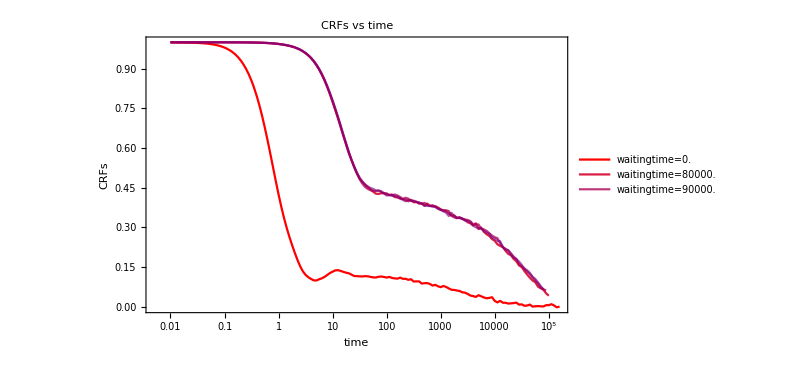

```mathematica
CRFswaitTime=ListLogLinearPlot[Table[Table[{timeLongest[[wt,t]],Mean[Table[SISF[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLongest[[wt]]]-1}],{wt,4}],FrameLabel->{"time","CRFs"},ImageSize->600,PlotLabel->"CRFs vs time",Joined->True,PlotStyle->redBluePlotConfig[7],PlotLegends->Table["waitingtime="<>ToString[wtlist[[wt]]],{wt,3}],PlotRange->All]
```

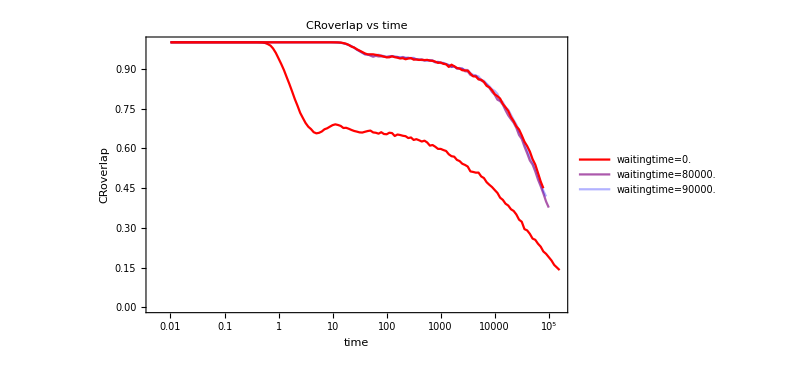

```mathematica
CRoverlapwaitTime=ListLogLinearPlot[Table[Table[{timeLongest[[wt,t]],Mean[Table[overlap[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLongest[[wt]]]-1}],{wt,4}],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time",Joined->True,PlotStyle->redBluePlotConfig[3],PlotLegends->Table["waitingtime="<>ToString[wtlist[[wt]]],{wt,3}],PlotRange->{All,{0,1}}]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlapwaitTimeLT.jpeg",CRoverlapwaitTimeLT,ImageResolution->600];
```

### the relaxation time for these low temperature

```mathematica
overlap=Table[Table[Import[StringJoin[saveFolder,"overlapCRoverlap_N4096_p3.8250_T",Tstring[[T]],"_waitingTime",wtlistLongestString[[T]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
Table[Length[overlap[[T,2,1]]],{T,Length[Tlist]}]
```

{91,91,91,91,92,101,105,111,117,126,129,129,129,129,129,130,130,130,131,130,130}

```mathematica
SISF=Table[Table[Import[StringJoin[saveFolder,"SISFCRSISF_N4096_p3.8250_T",Tstring[[T]],"_waitingTime",wtlistLongestString[[T]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
CRoverlapMean=Table[Table[Mean[Table[overlap[[T,i,2,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
overlapMean=Table[Table[Mean[Table[overlap[[T,i,1,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
```

```mathematica
CRSISFMean=Table[Table[Mean[Table[SISF[[T,i,2,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
```

```mathematica
SISFMean=Table[Table[Mean[Table[SISF[[T,i,1,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
```

```mathematica
testdata=Import[StringJoin[saveFolder,"glassyDynamics_N4096_p3.8250_T",Tstring[[21]],"_waitingTime",wtlistLongestString[[21]],"_idx0.nc"],"Data"];time=Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}];
```

```mathematica
Length[time]
```

130

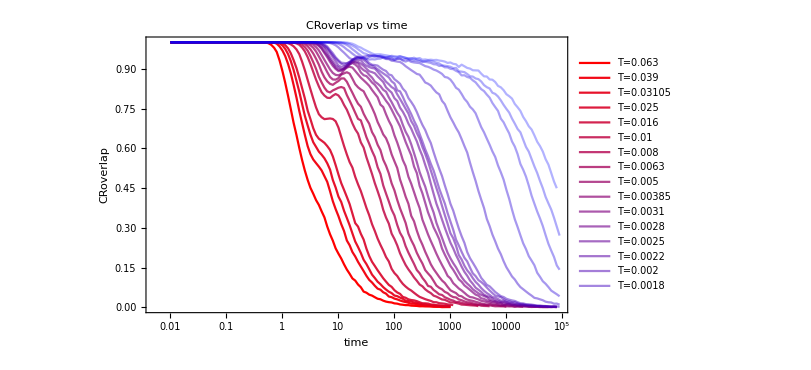

```mathematica
CRoverlapPlot=ListLogLinearPlot[Table[Table[{time[[rec]],CRoverlapMean[[T,rec]]},{rec,Length[CRoverlapMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time",Joined->True]
```

```mathematica
fitCROverlapStartNum={5.948031489453049,8.249631324484659,9.809422808922232,11.00988365852913,15.869275618720037,22.00991596517457,26.67987828722697,27.198214213949562,31.724351830515605,39.202590243884316,44.00013804131015,48.44364007940446,45.72641261596722,50.344248302369664,57.60307694378264,61.026058404512504,57.60307694378264,72.56450448580995,75.41145598852647,81.44482786499032,91.41191045072242};
```

```mathematica
fitCROverlapStartPos=Table[Position[time,_?(#>fitCROverlapStartNum[[i]]&)][[1,1]],{i,Length[Tlist]}]
```

{47,50,51,52,56,58,60,60,62,63,64,65,65,66,67,67,67,69,69,70,71}

```mathematica
fitsCROverlap=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRoverlapMean[[T,rec]]]},{rec,fitCROverlapStartPos[[T]],Length[CRoverlapMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,0.99>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsCROverlap
```

{FittedModel[0.989919 ⅇ^(-0.467709 t^0.525191)],FittedModel[0.989964 ⅇ^(-0.320356 t^0.536799)],FittedModel[0.989975 ⅇ^(-0.238958 t^0.574886)],FittedModel[0.98998 ⅇ^(-0.186368 t^0.592517)],FittedModel[0.989987 ⅇ^(-0.114314 t^0.617777)],FittedModel[0.989995 ⅇ^(-0.0550039 t^0.684225)],FittedModel[0.989995 ⅇ^(-0.0436927 t^0.683785)],FittedModel[0.989997 ⅇ^(-0.0321165 t^0.696583)],FittedModel[0.989997 ⅇ^(-0.0206882 t^0.72846)],FittedModel[0.989998 ⅇ^(-0.0136818 t^0.74848)],FittedModel[0.989998 ⅇ^(-0.0106297 t^0.747547)],FittedModel[0.989999 ⅇ^(-0.00911839 t^0.751123)],FittedModel[0.989998 ⅇ^(-0.00727941 t^0.754737)],FittedModel[0.989998 ⅇ^(-0.00621415 t^0.759504)],FittedModel[0.989999 ⅇ^(-0.00605749 t^0.747961)],FittedModel[0.989999 ⅇ^(-0.00453248 t^0.762584)],FittedModel[0.989989 ⅇ^(-0.00178035 t^0.75488)],FittedModel[0.968583 ⅇ^(-0.000696501 t^0.761602)],FittedModel[0.947473 ⅇ^(-0.000183215 t^0.815912)],FittedModel[0.950239 ⅇ^(-0.000246339 t^0.748264)],FittedModel[0.949858 ⅇ^(-0.000185292 t^0.735781)]}

```mathematica
tauCROverlapfits=Table[fitsCROverlap[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{4.25,8.33594,12.0613,17.0374,33.4705,69.3306,97.3488,139.223,205.166,309.164,436.453,520.047,680.217,804.157,922.582,1183.91,4388.28,13973.8,38036.3,66443.3,118129.}

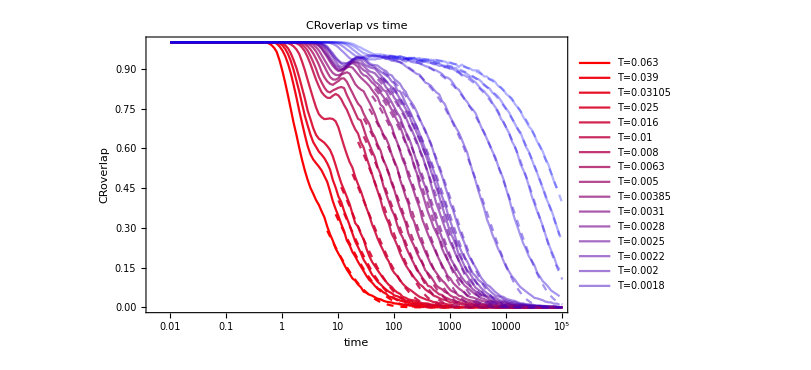

```mathematica
Show[CRoverlapPlot,Table[LogLinearPlot[fitsCROverlap[[T]][x],{x,time[[fitCROverlapStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

### overlap

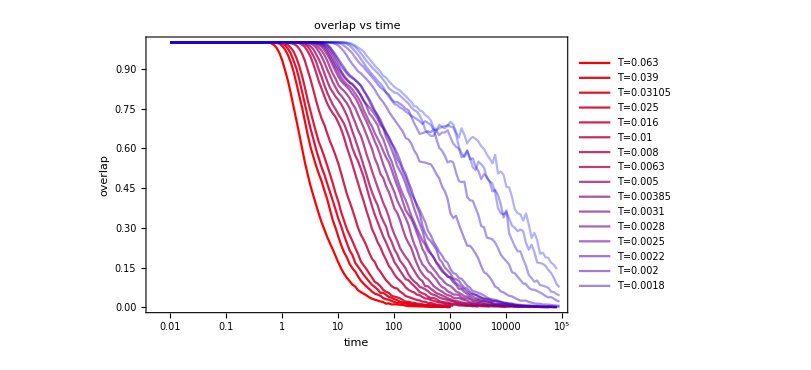

-Graphics-

```mathematica
overlapPlot=ListLogLinearPlot[Table[Table[{time[[rec]],overlapMean[[T,rec]]},{rec,Length[CRoverlapMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs time",Joined->True]
```

```mathematica
Length[fitOverlapStartNum]
```

0

```mathematica
fitOverlapStartNum={3.1775474914003787,4.762382435388608,5.6641934220626,6.867838653131914,9.529705899902194,13.480534523487432,15.4271079625378,17.998243599081505,20.997893671225114,25.459961382653482,28.034882793694486,31.470812087195352,33.992315823220075,33.992315823220075,34.65364754590804,35.,416.1470898512165,577.43921744198,848.9268952511062,1155.477535025538,1572.724743929531};
```

```mathematica
fitOverlapStartPos=Table[Position[time,_?(#>fitOverlapStartNum[[i]]&)][[1,1]],{i,Length[Tlist]}]
```

{42,45,47,48,51,54,55,57,58,60,60,61,62,62,62,62,84,87,90,93,95}

```mathematica
fitsOverlap=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[overlapMean[[T,rec]]]},{rec,fitOverlapStartPos[[T]],Length[overlapMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,0.9>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsOverlap
```

{FittedModel[0.899979 ⅇ^(-0.362302 t^0.646545)],FittedModel[0.899989 ⅇ^(-0.235077 t^0.691675)],FittedModel[0.899988 ⅇ^(-0.219032 t^0.653031)],FittedModel[0.899991 ⅇ^(-0.185269 t^0.655213)],FittedModel[0.899994 ⅇ^(-0.132067 t^0.658253)],FittedModel[0.899996 ⅇ^(-0.0697723 t^0.726266)],FittedModel[0.899997 ⅇ^(-0.0563617 t^0.722359)],FittedModel[0.899997 ⅇ^(-0.0557028 t^0.686872)],FittedModel[0.899998 ⅇ^(-0.041783 t^0.706025)],FittedModel[0.899997 ⅇ^(-0.0327012 t^0.704756)],FittedModel[0.899998 ⅇ^(-0.0257662 t^0.715305)],FittedModel[0.899998 ⅇ^(-0.0254595 t^0.685495)],FittedModel[0.899999 ⅇ^(-0.0259708 t^0.659372)],FittedModel[0.899999 ⅇ^(-0.0168372 t^0.719098)],FittedModel[0.899999 ⅇ^(-0.0164739 t^0.702076)],FittedModel[0.899999 ⅇ^(-0.0220285 t^0.643046)],FittedModel[0.899991 ⅇ^(-0.0175267 t^0.561845)],FittedModel[0.899995 ⅇ^(-0.0172787 t^0.494087)],FittedModel[0.753341 ⅇ^(-0.00126729 t^0.70483)],FittedModel[0.89998 ⅇ^(-0.0157985 t^0.439831)],FittedModel[0.841309 ⅇ^(-0.00367642 t^0.553706)]}

```mathematica
tauOverlapfits=Table[fitsOverlap[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{4.80814,8.11114,10.2305,13.1068,21.6603,39.0967,53.5893,66.9647,89.7817,128.153,166.479,211.614,253.852,292.823,346.657,377.419,1336.45,3691.19,12894.,12463.1,24938.7}

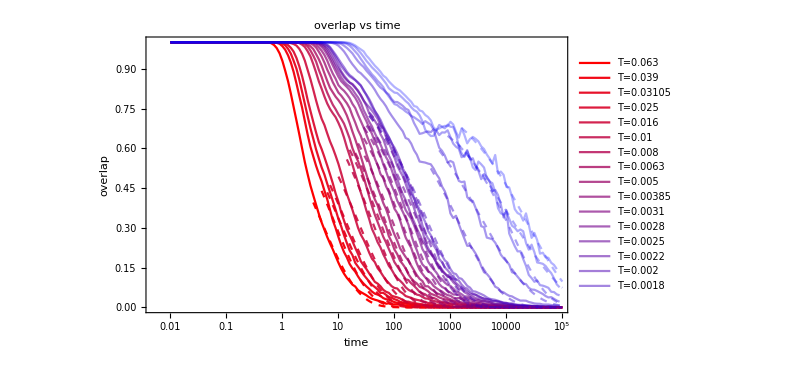

```mathematica
Show[overlapPlot,Table[LogLinearPlot[fitsOverlap[[T]][x],{x,time[[fitOverlapStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlap.jpeg",Show[CRoverlapfitST,CRoverlapLTPlot,Table[LogLinearPlot[fitsCRoverlapLT[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]+Length[TlistLT]][[T+Length[Tlist]]]}],{T,Length[TlistLT]}]],ImageResolution->600];
```

Show::gcomb: Could not combine the graphics objects in Show[CRoverlapfitST,CRoverlapLTPlot,{}].

#### CRSISF

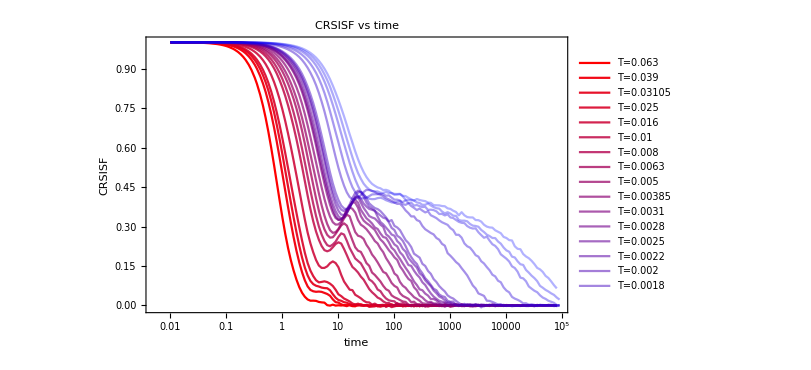

```mathematica
CRSISFPlot=ListLogLinearPlot[Table[Table[{time[[rec]],CRSISFMean[[T,rec]]},{rec,Length[CRSISFMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time",Joined->True]
```

```mathematica
fitCRSISFStartNum={6.421020423262568,10.650828740730146,12.458832828182784,14.576026130799443,19.924443715687687,26.237572659796527,28.976232281437134,37.38913876160977,47.243690497792436,59.69091806663826,63.323102094246536,67.20778364461461,100.,100.,100.,100.,100.,100.,100.,100.,100.};
```

```mathematica
fitCRSISFStartPos=Table[Position[time,_?(#>fitCRSISFStartNum[[i]]&)][[1,1]],{i,Length[Tlist]}]
```

{48,52,53,55,57,60,61,63,65,67,68,68,72,72,72,72,72,72,72,72,72}

```mathematica
fitsCRSISF=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRSISFMean[[T,rec]]]},{rec,fitCRSISFStartPos[[T]],Length[CRSISFMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsCRSISF
```

{FittedModel[0.198937 ⅇ^(-1.1598 t^0.768925)],FittedModel[0.275628 ⅇ^(-0.76724 t^0.736949)],FittedModel[0.5759 ⅇ^(-0.397072 t^0.892514)],FittedModel[0.581563 ⅇ^(-0.316944 t^0.893911)],FittedModel[0.385609 ⅇ^(-0.153387 t^0.892031)],FittedModel[0.595712 ⅇ^(-0.1059 t^0.852083)],FittedModel[0.458113 ⅇ^(-0.0642605 t^0.877795)],FittedModel[0.365488 ⅇ^(-0.0380795 t^0.898629)],FittedModel[0.411216 ⅇ^(-0.0272734 t^0.899489)],FittedModel[0.596161 ⅇ^(-0.0423961 t^0.782233)],FittedModel[0.446333 ⅇ^(-0.0142476 t^0.899895)],FittedModel[0.484834 ⅇ^(-0.0195654 t^0.817801)],FittedModel[0.405703 ⅇ^(-0.00873705 t^0.899722)],FittedModel[0.418534 ⅇ^(-0.00870318 t^0.87402)],FittedModel[0.513474 ⅇ^(-0.0159781 t^0.781821)],FittedModel[0.463765 ⅇ^(-0.0102687 t^0.805044)],FittedModel[0.43785 ⅇ^(-0.00363049 t^0.78683)],FittedModel[0.422065 ⅇ^(-0.00217756 t^0.739627)],FittedModel[0.40277 ⅇ^(-0.0011905 t^0.713063)],FittedModel[0.428989 ⅇ^(-0.00351694 t^0.579821)],FittedModel[0.4301 ⅇ^(-0.00330701 t^0.553027)]}

```mathematica
tauCRSISFfits=Table[fitsCRSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{0.824644,1.43266,2.81475,3.6161,8.18017,13.9436,22.804,37.9678,54.8345,56.861,112.626,122.787,194.124,227.664,198.521,295.142,1262.1,3973.31,12618.3,17062.9,30579.8}

```mathematica
Length[TlistLongest]
```

0

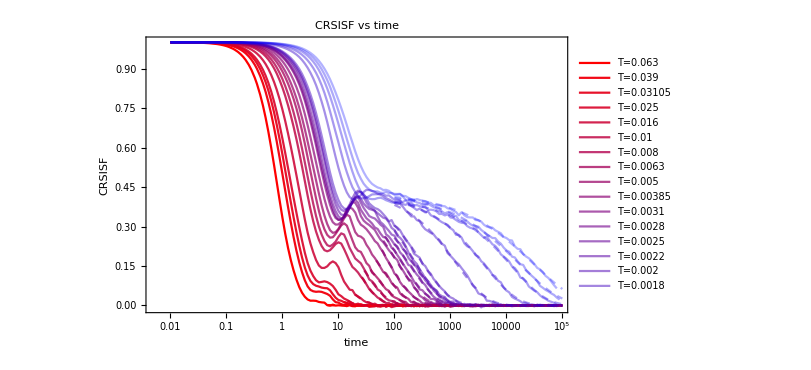

```mathematica
Show[CRSISFPlot,Table[LogLinearPlot[fitsCRSISF[[T]][x],{x,fitCRSISFStartNum[[T]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/CRSISF_p380.jpeg",Show[CRSISFSTLTwithFitPlot,CRSISFLongestPlot,Table[LogLinearPlot[fitsCRSISFLongest[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T+Length[Tlist]+Length[TlistLT]]]}],{T,Length[TlistLongest]}]]];
```

Show::gcomb: Could not combine the graphics objects in Show[CRSISFSTLTwithFitPlot,CRSISFLongestPlot,{}].

#### SISF

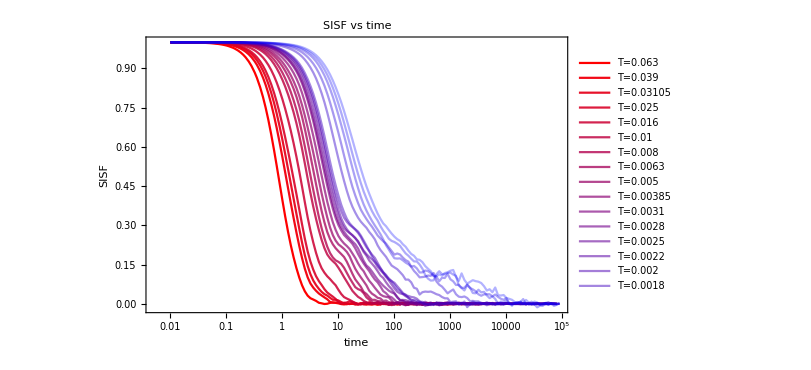

```mathematica
SISFPlot=ListLogLinearPlot[Table[Table[{time[[rec]],SISFMean[[T,rec]]},{rec,Length[SISFMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","SISF"},ImageSize->600,PlotLabel->"SISF vs time",Joined->True]
```

```mathematica
fitSISFStartNum={3.1775474914003787,3.7071286424358783,4.004151124598949,4.671496921073785,6.358391726586881,9.715109473235286,12.242387132886902,13.74280277156845,16.98734562378753,19.81851591245516,23.121538919078386,25.459961382653482,31.470812087195352,31.470812087195352,36.7158474278988,39.657593773822654,55.0282591729173,73.46978798963367,77.8418930594216,108.01219787096224,123.609033078256}
```

{3.17755,3.70713,4.00415,4.6715,6.35839,9.71511,12.2424,13.7428,16.9873,19.8185,23.1215,25.46,31.4708,31.4708,36.7158,39.6576,55.0283,73.4698,77.8419,108.012,123.609}

```mathematica
fitSISFStartPos=Table[Position[time,_?(#>fitSISFStartNum[[i]]&)][[1,1]],{i,Length[Tlist]}]
```

{42,43,44,45,48,51,53,54,56,57,59,60,61,61,63,63,66,69,69,72,73}

```mathematica
fitsSISF=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[SISFMean[[T,rec]]]},{rec,fitSISFStartPos[[T]],Length[SISFMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,0.5>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsSISF
```

{FittedModel[0.492229 ⅇ^(-1.13825 t^0.896548)],FittedModel[0.483939 ⅇ^(-0.663317 t^0.889042)],FittedModel[0.330679 ⅇ^(-0.46509 t^0.892869)],FittedModel[0.499427 ⅇ^(-0.463618 t^0.899603)],FittedModel[0.499814 ⅇ^(-0.286001 t^0.89987)],FittedModel[0.49991 ⅇ^(-0.167103 t^0.899916)],FittedModel[0.49929 ⅇ^(-0.134025 t^0.899422)],FittedModel[0.499911 ⅇ^(-0.111356 t^0.899877)],FittedModel[0.49986 ⅇ^(-0.0887455 t^0.899856)],FittedModel[0.495792 ⅇ^(-0.080793 t^0.856033)],FittedModel[0.439043 ⅇ^(-0.051391 t^0.899339)],FittedModel[0.365844 ⅇ^(-0.0438176 t^0.874659)],FittedModel[0.419982 ⅇ^(-0.0364484 t^0.899804)],FittedModel[0.358239 ⅇ^(-0.0275202 t^0.899537)],FittedModel[0.49952 ⅇ^(-0.0741493 t^0.704438)],FittedModel[0.387323 ⅇ^(-0.0333794 t^0.854698)],FittedModel[0.499944 ⅇ^(-0.122274 t^0.506962)],FittedModel[0.394849 ⅇ^(-0.076283 t^0.483295)],FittedModel[0.330153 ⅇ^(-0.123686 t^0.348412)],FittedModel[0.499838 ⅇ^(-0.196101 t^0.316536)],FittedModel[0.49985 ⅇ^(-0.223744 t^0.276814)]}

```mathematica
tauSISFfits=Table[fitsSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{0.865516,1.58682,2.35697,2.35016,4.01904,7.30184,9.34153,11.4644,14.7541,18.8966,27.1269,35.7279,39.6719,54.2766,40.1757,53.3994,63.1344,205.306,402.897,171.868,223.383}

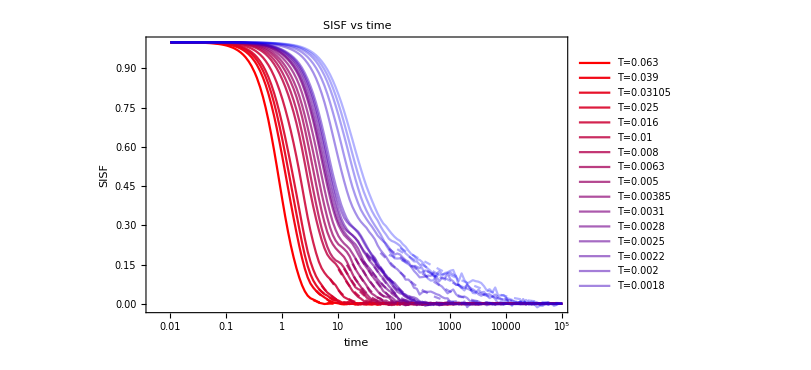

```mathematica
Show[SISFPlot,Table[LogLinearPlot[fitsSISF[[T]][x],{x,time[[fitSISFStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

#### Tau Alphas

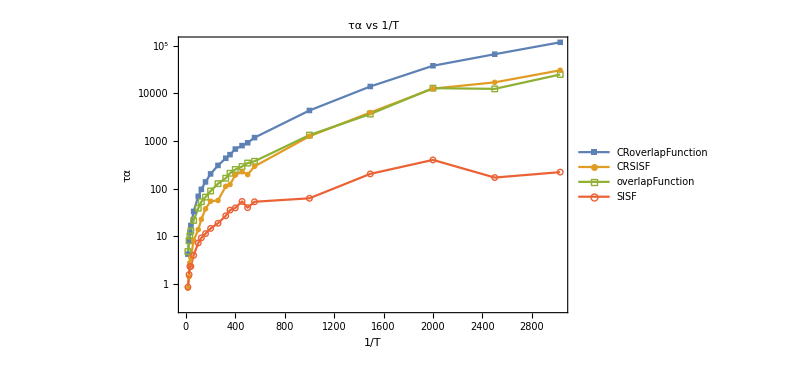

```mathematica
tauAlphafitingPlot=ListLogPlot[{Table[{1/Tlist[[T]],tauCROverlapfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauCRSISFfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauOverlapfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauSISFfits[[T]]},{T,Length[Tlist]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF","overlapFunction","SISF"},PlotMarkers->{Style["■",Large],Style["●",Large],Style["□",Large],Style["○",Large]},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
tauTable=Prepend[Table[{Tlist[[T]],tauCRSISFfits[[T]],tauCROverlapfits[[T]],tauOverlapfits[[T]],tauSISFfits[[T]]},{T,Length[Tlist]}],{"T","τα CRSISF","τα CR overlap","τα SISF","τα overlap"}]
```

{{T,τα CRSISF,τα CR overlap,τα SISF,τα overlap},{0.063,0.824644,4.25,4.80814,0.865516},{0.039,1.43266,8.33594,8.11114,1.58682},{0.03105,2.81475,12.0613,10.2305,2.35697},{0.025,3.6161,17.0374,13.1068,2.35016},{0.016,8.18017,33.4705,21.6603,4.01904},{0.01,13.9436,69.3306,39.0967,7.30184},{0.008,22.804,97.3488,53.5893,9.34153},{0.0063,37.9678,139.223,66.9647,11.4644},{0.005,54.8345,205.166,89.7817,14.7541},{0.00385,56.861,309.164,128.153,18.8966},{0.0031,112.626,436.453,166.479,27.1269},{0.0028,122.787,520.047,211.614,35.7279},{0.0025,194.124,680.217,253.852,39.6719},{0.0022,227.664,804.157,292.823,54.2766},{0.002,198.521,922.582,346.657,40.1757},{0.0018,295.142,1183.91,377.419,53.3994},{0.001,1262.1,4388.28,1336.45,63.1344},{0.00067,3973.31,13973.8,3691.19,205.306},{0.0005,12618.3,38036.3,12894.,402.897},{0.0004,17062.9,66443.3,12463.1,171.868},{0.00033,30579.8,118129.,24938.7,223.383}}

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP3825.csv",tauTable,"CSV"]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP3825.csv

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha_p380.jpeg",tauAlphafitingPlot];
```

```mathematica
Export["/home/chengling/Research/updates/02012024/taualpha.jpeg",tauAlphafitingPlot,ImageResolution->600];
```

```mathematica
betaCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

{0.809979,0.796758,0.809037,0.809862,0.80979,0.809928,0.80995,0.809939,0.809968,0.80997,0.809986,0.809967,0.809928,0.703551,0.771414,0.809972,0.809195,0.809984,0.793789,0.809994,0.809994,0.809994,0.794059}

```mathematica
GCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

{0.449978,0.437055,0.448006,0.449785,0.449754,0.449922,0.449957,0.449934,0.449975,0.449977,0.44999,0.449993,0.441588,0.473171,0.454078,0.449017,0.44834,0.455473,0.448606,0.457386,0.45083,0.452285,0.449566}

```mathematica
betaCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

{0.529141,0.592079,0.569808,0.630995,0.641043,0.665991,0.691322,0.701875,0.704992,0.729689,0.738498,0.762204,0.759353,0.730815,0.74279,0.794476,0.764024,0.795187,0.765277,0.801778,0.865234,0.912167,0.836894}

```mathematica
GCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

{0.999912,0.999974,0.999974,0.999988,0.999992,0.999993,0.999996,0.999996,0.999997,0.999996,0.999997,0.999998,0.980185,0.993608,0.988459,0.976593,0.980814,0.978599,0.973606,0.976955,0.965694,0.961696,0.962681}

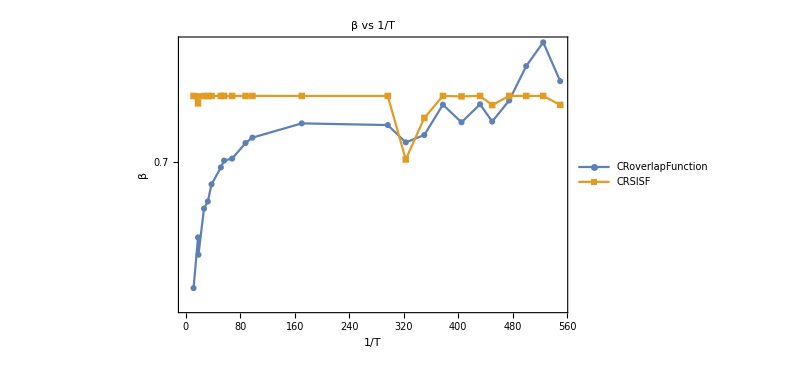

```mathematica
betafitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],betaCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],betaCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","β"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"β vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingBeta_p380_p380.jpeg",betafitingPlot,ImageResolution->600];
```

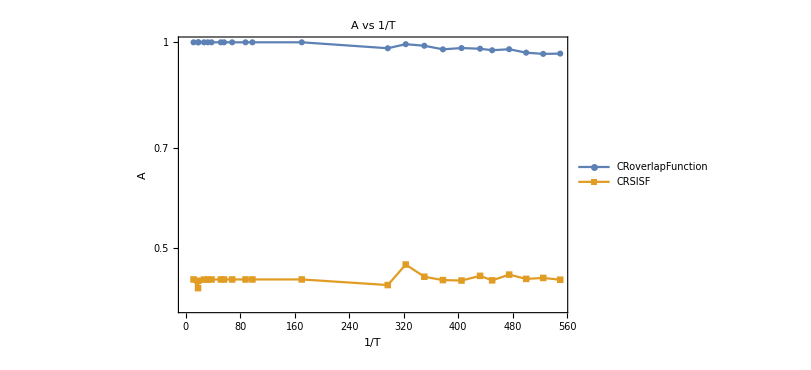

```mathematica
GfitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],GCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],GCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","A"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"A vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingA_p380_p380.jpeg",GfitingPlot,ImageResolution->600];
```

```mathematica
tauCRSISFAllT
```

{0.728537,1.41524,1.61389,2.6929,4.03698,5.21129,9.19522,9.51448,14.8936,25.9793,32.3344,138.256,1036.02,1239.22,2019.54,2804.8,4144.73,5262.53,6834.04,9346.07,13224.1,18754.3,19569.1}

```mathematica
tauTable=Prepend[Table[{TlistAllT[[T]],tauCRSISFAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],{"T","τα CRSISF","τα CR overlap"}]
```

{{T,τα CRSISF,τα CR overlap},{0.08868,0.728537,3.16039},{0.05586,1.41524,6.7635},{0.05409,1.61389,6.75448},{0.03756,2.6929,12.5106},{0.03105,4.03698,17.4891},{0.02652,5.21129,23.0389},{0.01945,9.19522,38.8819},{0.01782,9.51448,42.9591},{0.01471,14.8936,64.5399},{0.01141,25.9793,101.84},{0.01023,32.3344,125.531},{0.005873,138.256,436.846},{0.003371,1036.02,2732.95},{0.00309559,1239.22,3582.02},{0.00285428,2019.54,5140.15},{0.00264787,2804.8,7160.55},{0.00246931,4144.73,10064.4},{0.0023133,5262.53,13246.9},{0.00222222,6834.04,17008.4},{0.00210526,9346.07,22594.2},{0.002,13224.1,29109.1},{0.00190476,18754.3,39352.1},{0.00181818,19569.1,46020.2}}

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv",tauTable,"CSV"]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv

```mathematica
NumberForm[#,{9,6},ExponentFunction->(Null&)]&/@TlistAllT
```

{0.088680,0.055860,0.054090,0.037560,0.031050,0.026520,0.019450,0.017820,0.014710,0.011410,0.010230,0.005873,0.003371,0.003096,0.002854,0.002648,0.002469,0.002313,0.002222,0.002105,0.002000,0.001905,0.001818}

```mathematica
TlistAllT
```

{0.08868,0.05586,0.05409,0.03756,0.03105,0.02652,0.01945,0.01782,0.01471,0.01141,0.01023,0.005873,0.003371,0.00309559,0.00285428,0.00264787,0.00246931,0.0023133,0.00222222,0.00210526,0.002,0.00190476,0.00181818}

```mathematica
TlistGeneral={0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.28,0.0025,0.0022,0.002,0.0018}
```

{0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.28,0.0025,0.0022,0.002,0.0018}

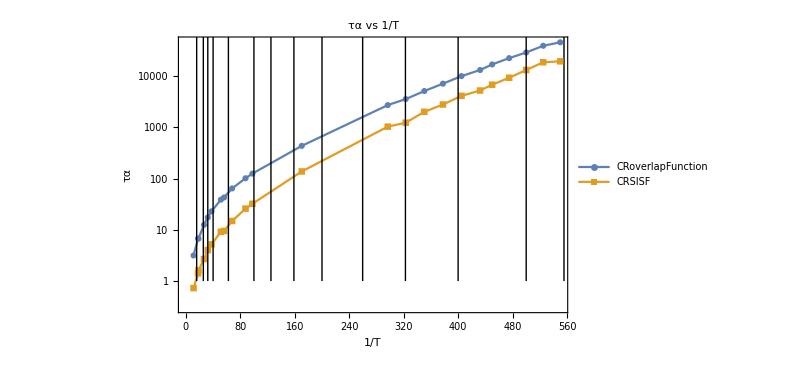

```mathematica
ListLogPlot[{Table[{1/TlistAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],tauCRSISFAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All,Epilog->Table[Line[{{1/TlistGeneral[[T]],0},{1/TlistGeneral[[T]],10000}}],{T,Length[TlistGeneral]}]]
```

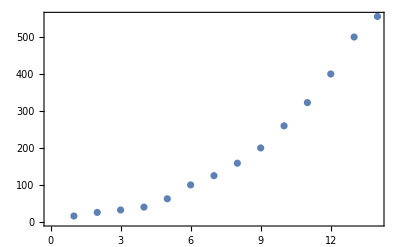

```mathematica
ListPlot[1/TlistGeneral]
```

```mathematica
tauEsGeneral={1.1841166706949628,2.462846296611076,3.8650575360708697,5.57413355409462,11.924841063370899,33.8105307104969,54.5761704083136,107.2953843344434,216.96587756816794,565.3189946945129,1243.945127271425,2065.,3731.3453237234366,7000.,12885.217184405017,22000.};
```

```mathematica
Length[TlistGeneral]
```

16